### e)

```mathematica
Solve[{y ==0,-Sin[x]-σ*y==0} ]
```

{{y→0,x→ConditionalExpression[2 π C[1], C[1]∈ℤ]},{y→0,x→ConditionalExpression[π+2 π C[1], C[1]∈ℤ]}}

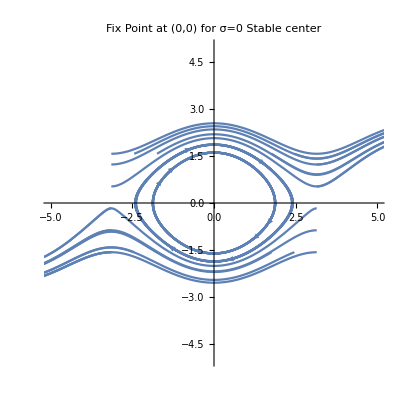

```mathematica
xmin = -π;
xmax = π;
ymin = -π/2;
ymax = π/2;
solution[x0_,y0_]:=Table[NDSolve[{D[x[t],t]==y[t], D[y[t],t]==-Sin[x[t]]-σ y[t],x[0]==x0,y[0]==y0},{x[t],y[t]},{t,0,15}],{σ,{0}}];
IC1 = Table[{xmin, y}, {y,ymin, ymax, 0.7}];
IC2 = Table[{xmax, y},{y,ymin, ymax,0.7}];
IC3 = Table[{x,ymin},{x,xmin,xmax,0.7}];
IC4 = Table[{x,ymax},{x, xmin, xmax, 0.7}];
ICs = Join[IC1, IC2, IC3, IC4];
plot = 
Table[ParametricPlot[
Evaluate[{x[t],y[t]}/.solution[ICs[[i,1]],ICs[[i,2]]]],{t,0,15}, PlotRange->{{-5,5},{-5,5}}, PlotLabel->"Fix Point at (0,0) for σ=0\n Stable center"]/. Line[x_]:>{Arrowheads[{0, 0.0375, 0.0375, 0}],Arrow[x]},{i,Length[ICs]}];
Show[{plot}]
```

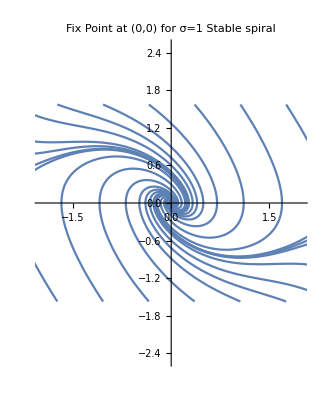

```mathematica
xmin = -π;
xmax = π;
ymin = -π/2;
ymax = π/2;
solution[x0_,y0_]:=Table[NDSolve[{D[x[t],t]==y[t], D[y[t],t]==-Sin[x[t]]-σ y[t],x[0]==x0,y[0]==y0},{x[t],y[t]},{t,0,15}],{σ,{1}}];
IC1 = Table[{xmin, y}, {y,ymin, ymax, 0.7}];
IC2 = Table[{xmax, y},{y,ymin, ymax,0.7}];
IC3 = Table[{x,ymin},{x,xmin,xmax,0.7}];
IC4 = Table[{x,ymax},{x, xmin, xmax, 0.7}];
ICs = Join[IC1, IC2, IC3, IC4];
plot = 
Table[ParametricPlot[
Evaluate[{x[t],y[t]}/.solution[ICs[[i,1]],ICs[[i,2]]]],{t,0,15}, PlotRange->{{-2,2},{-2.5,2.5}}, PlotLabel->"Fix Point at (0,0) for σ=1\n Stable spiral"]/. Line[x_]:>{Arrowheads[{0, 0.0375, 0.0375, 0}],Arrow[x]},{i,Length[ICs]}];
Show[{plot}]
```

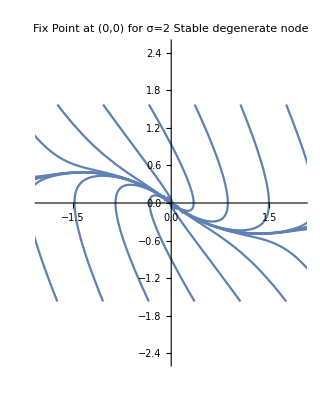

```mathematica
xmin = -π;
xmax = π;
ymin = -π/2;
ymax = π/2;
solution[x0_,y0_]:=Table[NDSolve[{D[x[t],t]==y[t], D[y[t],t]==-Sin[x[t]]-σ y[t],x[0]==x0,y[0]==y0},{x[t],y[t]},{t,0,15}],{σ,{2}}];
IC1 = Table[{xmin, y}, {y,ymin, ymax, 0.7}];
IC2 = Table[{xmax, y},{y,ymin, ymax,0.7}];
IC3 = Table[{x,ymin},{x,xmin,xmax,0.7}];
IC4 = Table[{x,ymax},{x, xmin, xmax, 0.7}];
ICs = Join[IC1, IC2, IC3, IC4];
plot = 
Table[ParametricPlot[
Evaluate[{x[t],y[t]}/.solution[ICs[[i,1]],ICs[[i,2]]]],{t,0,15}, PlotRange->{{-2,2},{-2.5,2.5}}, PlotLabel->"Fix Point at (0,0) for σ=2\n Stable degenerate node "]/. Line[x_]:>{Arrowheads[{0, 0.0375, 0.0375, 0}],Arrow[x]},{i,Length[ICs]}];
Show[{plot}]
```

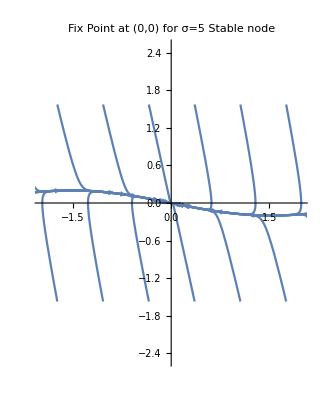

```mathematica
xmin = -π;
xmax = π;
ymin = -π/2;
ymax = π/2;
solution[x0_,y0_]:=Table[NDSolve[{D[x[t],t]==y[t], D[y[t],t]==-Sin[x[t]]-σ y[t],x[0]==x0,y[0]==y0},{x[t],y[t]},{t,0,15}],{σ,{5}}];
IC1 = Table[{xmin, y}, {y,ymin, ymax, 0.7}];
IC2 = Table[{xmax, y},{y,ymin, ymax,0.7}];
IC3 = Table[{x,ymin},{x,xmin,xmax,0.7}];
IC4 = Table[{x,ymax},{x, xmin, xmax, 0.7}];
ICs = Join[IC1, IC2, IC3, IC4];
plot = 
Table[ParametricPlot[
Evaluate[{x[t],y[t]}/.solution[ICs[[i,1]],ICs[[i,2]]]],{t,0,15}, PlotRange->{{-2,2},{-2.5,2.5}}, PlotLabel->"Fix Point at (0,0) for σ=5\n Stable node "]/. Line[x_]:>{Arrowheads[{0, 0.0375, 0.0375, 0}],Arrow[x]},{i,Length[ICs]}];
Show[{plot}]
```

```mathematica
textgrid = TextGrid[{{"Fixed point @","(0,0)"}, {"(σ=0)","Stable center"},
{"(σ=1)","Stable spiral"},{"(σ=2)","Stable degenerate node"},{"(σ=5)","Stable node"}},Frame->All]
Export["C:/Users/maxim/OneDrive/Dokument/Wolfram Mathematica/TIF155/TIF155-Problems/Problem set 2table.png",textgrid];
```

Fixed point @ | (0,0)
(σ=0) | Stable center
(σ=1) | Stable spiral
(σ=2) | Stable degenerate node
(σ=5) | Stable node